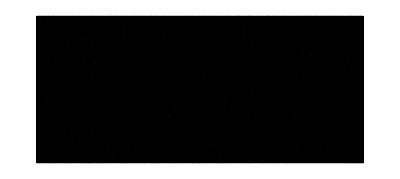

12996

```mathematica
configPath="D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\";
Mcm=0.5;
(*TO DO: Fix the borders and source and MCM*)
left=0;
right=134;
lower=-60;
middle=-3;
upper=0;
region=Rectangle[{left,lower},{right,upper}];
Needs["NDSolve`FEM`"];
em=ToElementMesh[region,"MeshOrder"->1,"MeshElementType"->"TriangleElement","MeshQualityGoal"->0.9,MaxCellMeasure->Mcm];
Show[em["Wireframe"]]
elements=em["MeshElements"][[1,1]];
nodes = em["Coordinates"];
elementsLen=Length[elements];
```

```mathematica
(*Check if mesh is ok*)
t = Table[{nodes[[i]],1},{i,1,Length[nodes]}];
(*Print["table: ",table];*)
intF = Interpolation[t,InterpolationOrder->1];
```

Interpolation::femimq: The element mesh has insufficient quality of -1.05569×10^-12. A quality estimate below 0. may be caused by a wrong ordering of element incidents or self-intersecting elements.

Interpolation::fememtlq: The quality -1.05569×10^-12 of the underlying mesh is too low. The quality needs to be larger than 0..

```mathematica
Length[elements]
Length[nodes]
getLongestEdgeInMesh[nodes,elements]
minLen
```

25440

12996

1.47902

0.621481

```mathematica
setUpMeshForCpp[nodes_, elements_]:=Module[{i,el,configFile, configLines,sourceElement, seismographNode, updatedLines,sourcep,eps,replacements,seismographn, sourcePointString},(
el=elements;
el -=1;
Export["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\nodes.csv",nodes,"CSV"];
Export["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\elements.csv",el,"CSV"];
Print["Exported nodes and elements"];
eps=getLongestEdgeInMesh[nodes,elements];
sourcep={findElementNearPoint[nodes,elements,67,-25.05,0.8]};
sourcePointString=ToString[sourcep[[1]] - 1];
Print["Found source"];

seismographn={findNodeNearPoint[nodes,elements,2.39,upper,eps,1],findNodeNearPoint[nodes,elements,31.11,upper,eps,1]};
seismograhmString=ToString[seismographn[[1]]-1];
seismograhmString =StringJoin[seismograhmString,", "];
seismograhmString=StringJoin[seismograhmString,ToString[seismographn[[2]]-1]];
Print["Resolved seismograh points"];

If[Length[inCavity]==0,cavityString=""];
configFile=configPath<>"config.txt";
configLines=Import[configFile,"Lines"];

depths=ToString[lower]<>", "<>ToString[middle]<>", "<>ToString[upper];
replacements=<|
"sourceElement"->sourcePointString,
"seismographIndices"->seismograhmString,
"depths"->ToString[depths],
"left"->ToString[left],
"right"->ToString[right]
|>;
updatedLines=configLines/.{line_/;StringContainsQ[line,"="]:>Module[{k,v},{k,v}=StringSplit[line,"=",2];
If[KeyExistsQ[replacements,k],Print[k];k<>"="<>replacements[k],line]]};

Export[configFile,updatedLines,"Lines"];
)]
```

```mathematica
nodes[[121]]
```

{30.,0.}

```mathematica
setUpMeshForCpp[nodes,elements]
```

Exported nodes and elements

Found source

Resolved seismograh points

StringContainsQ::strse: String or list of strings expected at position 1 in StringContainsQ[List,=].

sourceElement

seismographIndices

depths

left

right

```mathematica
nodes[[elements[[8427]]]]
```

{{67.6073,-25.1548},{67.6862,-24.3213},{66.8414,-24.2529}}

```mathematica
seismogram=Import["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\results\\Eigen_seismogram_displ_vel_0.5SPECFEMNEW.csv","CSV"];
Dimensions[seismogram]
```

{18465,8}

Hz=0.8

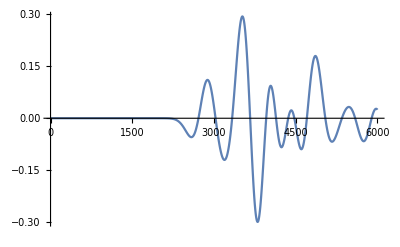

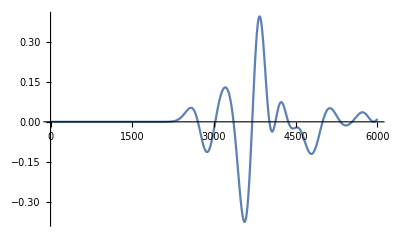

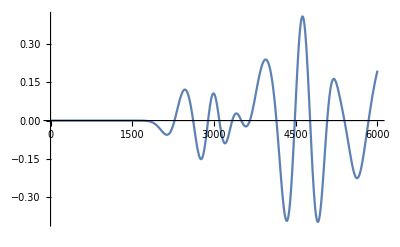

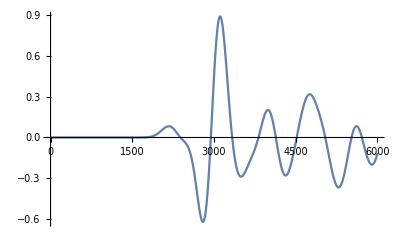

```mathematica
Print["Hz=0.8"]
finalPoint=6000;
ListLinePlot[seismogram[[1;;finalPoint,1]],PlotRange->All]
ListLinePlot[seismogram[[1;;finalPoint,2]],PlotRange->All]
ListLinePlot[seismogram[[1;;finalPoint,5]],PlotRange->All]
ListLinePlot[seismogram[[1;;finalPoint,6]],PlotRange->All]
```

Hz=0.8

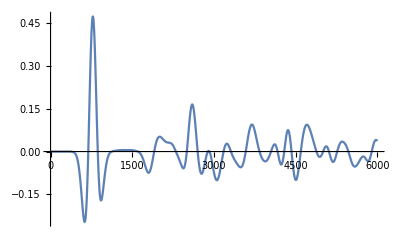

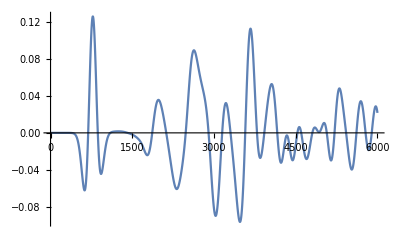

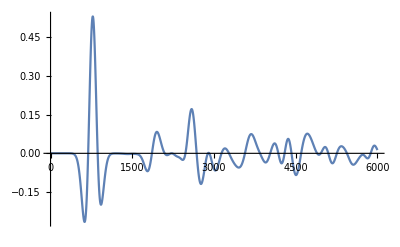

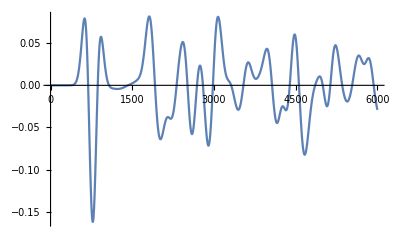

```mathematica
Print["Hz=0.8"]
ListLinePlot[seismogram[[1;;6000,1]],PlotRange->All]
ListLinePlot[seismogram[[1;;6000,2]],PlotRange->All]
ListLinePlot[seismogram[[1;;6000,5]],PlotRange->All]
ListLinePlot[seismogram[[1;;6000,6]],PlotRange->All]
```

Hz=0.4

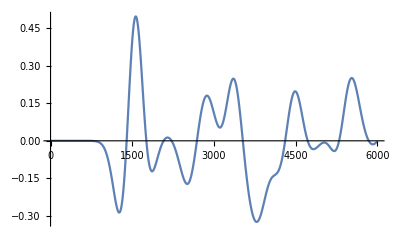

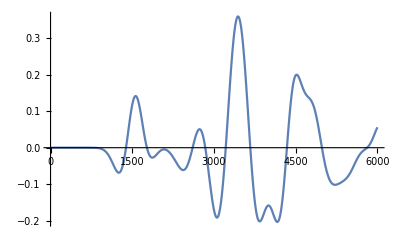

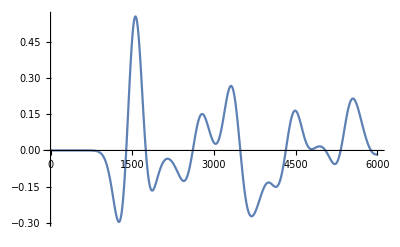

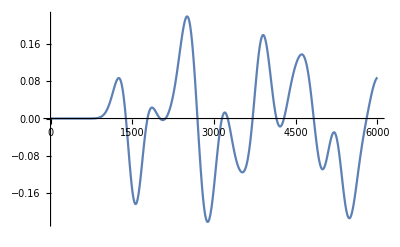

```mathematica
Print["Hz=0.4"]
ListLinePlot[seismogram[[1;;6000,1]]]
ListLinePlot[seismogram[[1;;6000,2]]]
ListLinePlot[seismogram[[1;;6000,5]]]
ListLinePlot[seismogram[[1;;6000,6]]]
```

```mathematica
Length[seismogram[[6]]]
```

8

```mathematica
nodes[[elements[[8318]]]]
```

{{68.3465,-25.7946},{68.3736,-24.8174},{67.6073,-25.1548}}

```mathematica
seismograhmString
```

89, 171

```mathematica
Dimensions[seismogram]
```

{18465,8}

```mathematica
nodes[[121]]
```

{30.,0.}

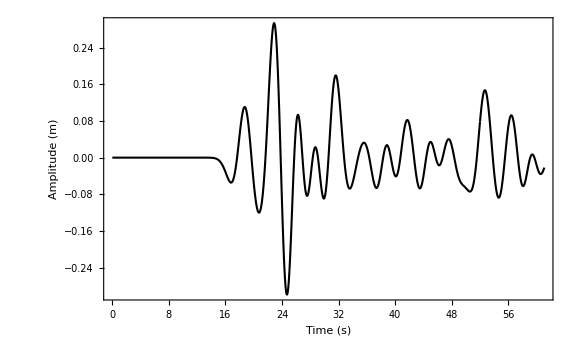

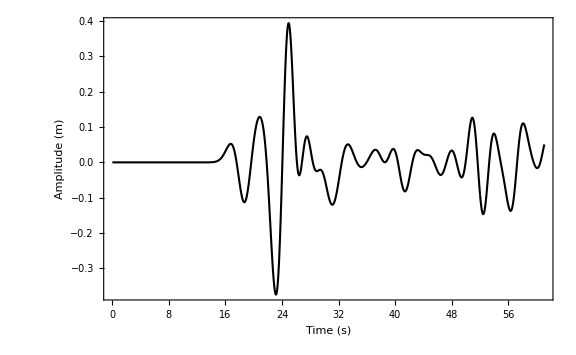

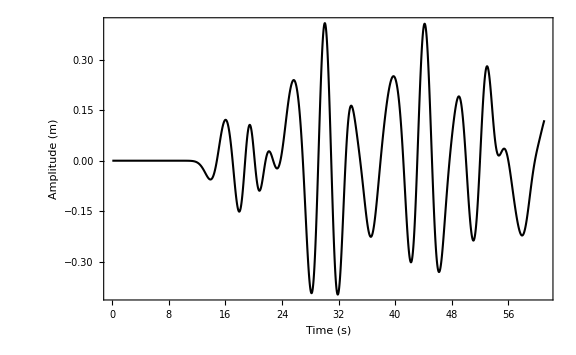

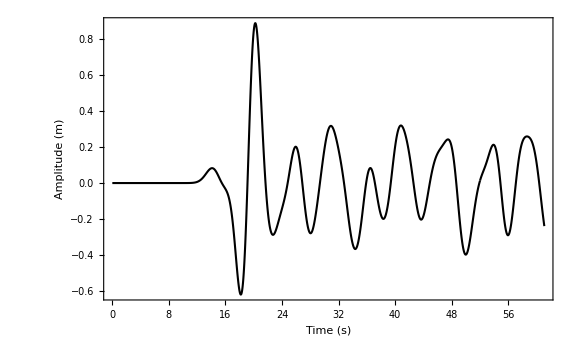

```mathematica
dt=0.0065;(*time step in seconds,adjust this*)
finalPoint=9400;
time=Range[0,(Length[seismogram[[1;;9400,1]]]-1)*dt,dt];
seismo1=ListLinePlot[Transpose[{time,seismogram[[1;;finalPoint,1]]}],Frame->True,FrameLabel->{"Time (s)","Amplitude (m)"},PlotStyle->{AbsoluteThickness[1.5],Black},LabelStyle->Directive[FontFamily->"Times",14],FrameTicks->{Automatic,Automatic},ImageSize->Large,PlotRange->All]
seismo2=ListLinePlot[Transpose[{time,seismogram[[1;;finalPoint,2]]}],Frame->True,FrameLabel->{"Time (s)","Amplitude (m)"},PlotStyle->{AbsoluteThickness[1.5],Black},LabelStyle->Directive[FontFamily->"Times",14],FrameTicks->{Automatic,Automatic},ImageSize->Large,PlotRange->All]
seismo3=ListLinePlot[Transpose[{time,seismogram[[1;;finalPoint,5]]}],Frame->True,FrameLabel->{"Time (s)","Amplitude (m)"},PlotStyle->{AbsoluteThickness[1.5],Black},LabelStyle->Directive[FontFamily->"Times",14],FrameTicks->{Automatic,Automatic},ImageSize->Large,PlotRange->All]
seismo4=ListLinePlot[Transpose[{time,seismogram[[1;;finalPoint,6]]}],Frame->True,FrameLabel->{"Time (s)","Amplitude (m)"},PlotStyle->{AbsoluteThickness[1.5],Black},LabelStyle->Directive[FontFamily->"Times",14],FrameTicks->{Automatic,Automatic},ImageSize->Large,PlotRange->All]
```

```mathematica
Export["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\Дипломна работа\\png\\seismo1.pdf",seismo1,"PDF","AllowRasterization"->False]
Export["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\Дипломна работа\\png\\seismo2.pdf",seismo2,"PDF","AllowRasterization"->False]
Export["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\Дипломна работа\\png\\seismo3.pdf",seismo3,"PDF","AllowRasterization"->False]
Export["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\Дипломна работа\\png\\seismo4.pdf",seismo4,"PDF","AllowRasterization"->False]
```

D:\Serious\FMI\Магистър\Дипломен семестър\Дипломна работа\png\seismo1.pdf

D:\Serious\FMI\Магистър\Дипломен семестър\Дипломна работа\png\seismo2.pdf

D:\Serious\FMI\Магистър\Дипломен семестър\Дипломна работа\png\seismo3.pdf

D:\Serious\FMI\Магистър\Дипломен семестър\Дипломна работа\png\seismo4.pdf